```mathematica
A1={{0,0},{0,(2 Di (R0^2/(-1+ρ0)-(ρ0 (ap c0^2 R0^2 κ+4 Λ-2 R0^2 χ))/kT))/R0^4}};
```

```mathematica
A2={{(6 (-pre R0^3+2 κ (-6+c0 R0 ρ0)))/(R0^4 (3 Γ1+2 Γ2)+8 R0^2 ηs),(12 c0 R0^2 κ)/(R0^4 (3 Γ1+2 Γ2)+8 R0^2 ηs)},{(24 ap c0 Di κ ρ0)/(kT R0^4),(6 Di (kT R0^2-(-1+ρ0) ρ0 (ap c0^2 R0^2 κ+12 Λ-2 R0^2 χ)))/(kT R0^4 (-1+ρ0))}};
```

```mathematica
A3={{-(15 (pre R0^3+24 κ-2 c0 R0 κ ρ0))/(R0^4 (3 Γ1+Γ2)+10 R0^2 ηs),(30 c0 R0^2 κ)/(R0^4 (3 Γ1+Γ2)+10 R0^2 ηs)},{(120 ap c0 Di κ ρ0)/(kT R0^4),(12 Di (kT R0^2-(-1+ρ0) ρ0 (ap c0^2 R0^2 κ+24 Λ-2 R0^2 χ)))/(kT R0^4 (-1+ρ0))}};
```

```mathematica
A4={{-(45 (pre R0^3+40 κ-2 c0 R0 κ ρ0))/(R0^4 (5 Γ1+Γ2)+18 R0^2 ηs),(90 c0 R0^2 κ)/(R0^4 (5 Γ1+Γ2)+18 R0^2 ηs)},{(360 ap c0 Di κ ρ0)/(kT R0^4),(20 Di (kT R0^2-(-1+ρ0) ρ0 (ap c0^2 R0^2 κ+40 Λ-2 R0^2 χ)))/(kT R0^4 (-1+ρ0))}};
```

```mathematica
subpara={R0->1,pre->0,κ->0.4,ρ0->0.2,Di->0.00312,kT->0.02,ap->0.01,Γ1->0,Γ2->0.01,ηs->1}
```

{R0→1,pre→0,κ→0.4,ρ0→0.2,Di→0.00312,kT→0.02,ap→0.01,Γ1→0,Γ2→0.01,ηs→1}

```mathematica
Simplify[Solve[Part[Eigenvalues[A1/.c0->0],1]==0,χ]]
```

{{χ→(2 Λ)/R0^2+kT/(2 ρ0-2 ρ0^2)}}

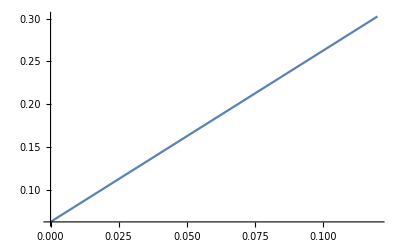

```mathematica
l1=Plot[(2 Λ)/R0^2+kT/(2 ρ0-2 ρ0^2)/.subpara,{Λ,0,0.12},PlotRange->All]
```